# Calculating Vectorial Capacity

## Introductory discussion

Vectorial Capacity is defined as “the number of infectious bites that arise from all the mosquitoes that are infected by a single infectious person on a single day.”  That is to say, we pick a single infectious person and look at all of the mosquitoes who bite that person on one day.  We then follow each of those mosquitoes and count the number of infectious bites that occur between the time when the mosquito becomes infectious (after the incubation period) and the time when the mosquito dies.

When it comes to our simplified model of mosquito movement, we will consider all of the infectious biting events to result in the transmission of a parasite from the host to the vector and from the vector to the host.  
	• We have no hosts in our model so we can’t say how likely each host is to be infected.  
	• We could of course add some assumptions about the efficiency of transfer from hosts to vectors, but those would only add some multiplicative constants to each infection event

We will also consider every single infection to be independent, such that every vector may be infected by an unbounded number of independent parasite strains.  This allows us to simply count the number of infectious bites that arise from *each* biting event

We will assume that each mosquito’s biological needs require it to fly between egg laying/resting sites and blood feeding sites.  (There are of course other types of sites where the mosquito might visit, but for now we will ignore these)

We will assume that every visit to a blood feeding site results in 1 bite of a host, and will treat each bite as transferring parasite from the host to the vector.  (Whether or not the bite results in transferring parasite from the infectious vector to the host is not relevant to how vectorial capacity is defined - only biting conditioning on being infectious, no biting conditioning on successful transmission.)

## Creating a landscape, defining transition matrix

The landscape will allow us to define a transition matrix which we can use as a Markov transitions matrix.

All of this is borrowed from Hector’s Walking Dead Malaria scripts

### Functions

```mathematica
SetDirectory[NotebookDirectory[]]
(*Movement Kernels*)
CalculateEuclideanDistances[coordinatesSet_]:=Table[N[EuclideanDistance[coordinatesSet[[i]],#]]&/@coordinatesSet,{i,1,coordinatesSet//Length }]
(* This one is out of date; use the exponential one instead:
CalculateInverseLinearKernelMigrationProbabilities[distancesMatrix_,nonMigratoryForce_]:=N[(#/Total[#])]&/@ReplaceAll[1/distancesMatrix//Quiet,ComplexInfinity->nonMigratoryForce] *)
ExponentialKernel[λ_,distance_]:=λ*ⅇ^(-λ*distance)
(*Markov - Calculates fraction of time mosquitoes spend at each network node, given a Markov process
migrationProbabilities = transitions probability matrix, calculated using Euclidean distances and a Kernel *)
CalculateMarkovSteadyState[migrationProbabilities_]:=Module[{initialState,markov,markovPDF},
initialState=ConstantArray[0,migrationProbabilities//Length]//ReplacePart[#,1->1]&;
markov=DiscreteMarkovProcess[initialState,migrationProbabilities];
markovPDF=PDF[StationaryDistribution[markov],#]&/@Range[markov[[1]]//Length];
markovPDF
]
(*Networks Plot*)
edgeshape[e_,___]:={Arrowheads[{{.0075,.5}}],Arrow[e]}
Options[EdgesStyleList]:={LineThickness->.004,VariableStyle->"Both"}
EdgesStyleList[vertexSyllableList_,OptionsPattern[]]:=Switch[OptionValue[VariableStyle],
"LineColor",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[1*vertexSyllableList[[i]][[2]]+.025],Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],
"LineWidth",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.5],Blue,Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],
"Both",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.75*vertexSyllableList[[i]][[2]]+.05],Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],_,Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}]]
VertexNumberToVertexSyllable[syllables_,fixedEdgesList_]:=Table[DirectedEdge[syllables[[fixedEdgesList[[index]][[1]][[1]]]],syllables[[fixedEdgesList[[index]][[1]][[2]]]]->fixedEdgesList[[index]][[2]]]//N,{index,1,Length[fixedEdgesList]}]
Options[GraphTransitionsFrequenciesWithMax]:={ImagePadding->None,Background->White,VertexStyle->Automatic,VertexCoordinates->Automatic,LineThickness->.0005,VariableStyle->"Both",GraphLayout->Automatic,Frame->False,FrameStyle->Thick,ImageSize->Automatic,VertexSize->.5,PlotTheme->"LakeNetwork",EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic},Prolog->{},Epilog->{},VertexShape->Automatic}
GraphTransitionsFrequenciesWithMax[frequenciesOutput_,max_,OptionsPattern[]]:=Module[{frequencies,syllables,edges,fixedEdgesList,vertexSyllableList,normalizedVertexSyllableList,edgesStyleList,links},frequencies=frequenciesOutput[[1]];
syllables=frequenciesOutput[[2]];
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[syllables]},{j,Length[syllables]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequenciesOutput[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList[normalizedVertexSyllableList,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle]];
links=DirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
Graph[syllables,links,
EdgeWeight->vertexSyllableList[[All,2,2]],
VertexStyle->OptionValue[VertexStyle],
EdgeStyle->edgesStyleList,
VertexCoordinates->OptionValue[VertexCoordinates],
ImageSize->OptionValue[ImageSize],
GraphLayout->OptionValue[GraphLayout],
EdgeShapeFunction->OptionValue[EdgeShapeFunction],
VertexShape->OptionValue[VertexShape],
VertexSize->OptionValue[VertexSize],
Frame->OptionValue[Frame],
FrameStyle->OptionValue[FrameStyle],
VertexLabelStyle->OptionValue[VertexLabelStyle],
VertexLabels->Placed["Name",Center],
EdgeLabels->Table[links[[i]]->Placed[fixedEdgesList[[All,2]][[i]],Tooltip],{i,Length[links]}],
Prolog->OptionValue[Prolog],
Epilog->OptionValue[Epilog],
Background->OptionValue[Background],
ImagePadding->OptionValue[ImagePadding],
PerformanceGoal->"Speed"
]
]
(*Plots Styles*)
Themes`AddThemeRules["LakeMatrixPlot"
,AspectRatio->1
,AxesStyle->Directive[Gray,Opacity[.5],Dashed]
,ColorFunction->ColorData[{"LakeColors","Reverse"}]
,Frame->True
,FrameStyle->Directive[Gray,Thick]
,FrameTicks->False
,ImageSize->250
,PlotRangePadding->0
]
Themes`AddThemeRules["LakeNetwork",
,EdgeShapeFunction->edgeshape2
,Epilog->Riffle[ConstantArray[Directive[Opacity[1],Lighter[Purple,.45],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]],sampledCoordinates//Length],(Disk[#,.25]&/@sampledCoordinates)]
,ImageSize -> 500
,ImagePadding->25
,LineThickness -> .0075
,VariableStyle->"Both"
,VertexCoordinates ->sampledCoordinates
,VertexSize ->.01
,VertexLabelStyle->.001
]
(*USES GLOBALS!*)
GraphPlotWrapper[migrationMatrix_,max_,vertexSize_,vertexStyle_]:= GraphTransitionsFrequenciesWithMax[
  {
migrationMatrix,
ToString /@ Range[Length[migrationMatrix]]
   }, max
,EdgeShapeFunction->edgeshape2
,ImagePadding->0
,ImageSize->imageSize
,LineThickness->lineThickness
,VariableStyle->"Both"
,VertexCoordinates->sampledCoordinates
,VertexSize -> vertexSize
,VertexStyle->vertexStyle
,VertexLabelStyle->.0001
  ]
```

/Users/dtcitron/Documents/MosPopDyn/MoNeT/MoNeT/Dev/DanielCitron

LakeMatrixPlot

LakeNetwork

### Inputs

#### Style

```mathematica
edgeChopThreshold=10^-1.5;
edgeshape2[e_,___]:={Arrowheads[{{.000000001,1}}],Arrow[e]}
lineThickness=.0005;
imageSize=250;
```

#### Parameters for generating landscape

```mathematica
(* Define:
nodesNumber - {size of grid, distance between nodes}, used as a way of generating all the different nodes on a grid;
 networkDimension - number of node types;
 distance - distance between cities;
*)
{nodesNumber,networkDimension,distance}={{100,50},2,50};
(**)
movementProbabilitiesVector=If[networkDimension>1,ConstantArray[0,networkDimension]//ReplacePart[#,{2->1,3->0}]&,ConstantArray[0,networkDimension]//ReplacePart[#,{1->1}]&];
(**)
penalizationsMatrix=Table[RotateRight[movementProbabilitiesVector,i-1],{i,1,networkDimension}];
MatrixForm[penalizationsMatrix]
```

(0 | 1
1 | 0)

#### Random Walks

```mathematica
{chainsSteps,chainsNumber}={20,30};
```

### Generate Landscape

```mathematica
citiesSqrt=Range[0,nodesNumber[[1]],nodesNumber[[2]]];
sampledCoordinates=Tuples[citiesSqrt,2];
clusteredCoordinates=FindClusters[sampledCoordinates,Method->"NeighborhoodContraction"];
euclideanDistances=CalculateEuclideanDistances[sampledCoordinates];
```

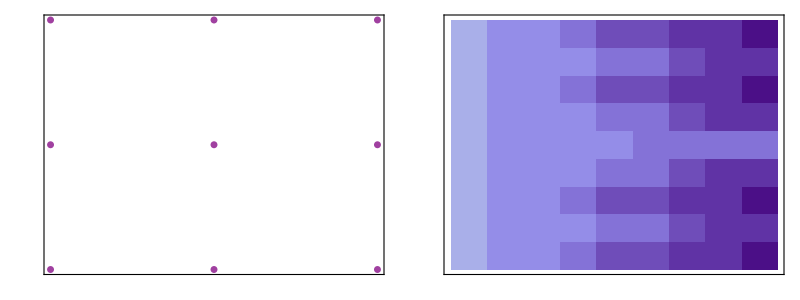

```mathematica
(*Visualize*)
colors=Reverse[ColorData["BrightBands",#]&/@Range[0,1,1/(Length[clusteredCoordinates])]]//Flatten//RandomSample;
gridCoordinatesPlot=ListPlot[clusteredCoordinates//Flatten[#,1]&
,AspectRatio->1
,AxesStyle->Directive[Gray,Opacity[.5],Dashed]
,GridLines->None
,GridLinesStyle->Directive[Gray,Opacity[.5],Dashed]
,ImageSize->250
,PlotRangePadding->.5
,PlotStyle->Directive[Purple,EdgeStyle[Black],Opacity[.75],PointSize[.02]]
,Frame->True
,FrameStyle->Directive[Gray,Thick]
,FrameTicks->False
,FrameTicksStyle->15
];
matrixDistancesPlot=MatrixPlot[Sort/@euclideanDistances,PlotTheme->"LakeMatrixPlot"];
Grid[{{gridCoordinatesPlot,matrixDistancesPlot}}]
```

### Movement Kernel

Use an exponential Kernel

```mathematica
migrationProbabilities=(#/Total[#])&/@ReplacePart[ExponentialKernel[0.01848777,#]&/@euclideanDistances,{i_,i_}->0];
```

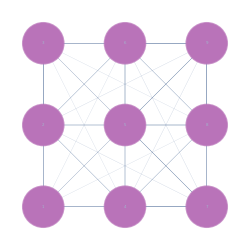

```mathematica
(*Visualize*)
matrixMigrationPlot=MatrixPlot[Sort/@migrationProbabilities,PlotTheme->"LakeMatrixPlot"];
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/networkDimension]];
stylesSwatchType=Directive[Opacity[1],Lighter[Purple,.45],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[networkDimension];
stylesListType=(ToString[#]->stylesSwatchType[[1]])&/@Range[migrationProbabilities//Length];
originalMap=GraphPlotWrapper[
Chop[migrationProbabilities//LowerTriangularize,.05*edgeChopThreshold],.1,
(#->.5)&/@(ToString/@Range[migrationProbabilities//Length]),
stylesListType
]
```

### Markov Baseline

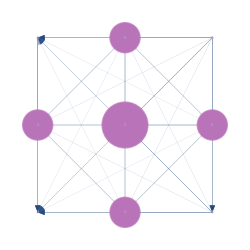

```mathematica
baselineMarkovSS=CalculateMarkovSteadyState[migrationProbabilities];
(*Visualize*)
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/networkDimension]];
stylesSwatchType=Directive[Opacity[1],Lighter[Purple,.45],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[networkDimension];
stylesListType=(ToString[#]->stylesSwatchType[[1]])&/@Range[migrationProbabilities//Length];
markovBaseline=GraphPlotWrapper[
Chop[migrationProbabilities//LowerTriangularize,.05*edgeChopThreshold],.1,
Thread[VertexList[originalMap ]->.25*Log[.5+7.5*Rescale[baselineMarkovSS]]],
stylesListType
]
```

### Network Dimensionality (aka n-partite-ness)

{2,1,1,1,1,2,1,2,1}

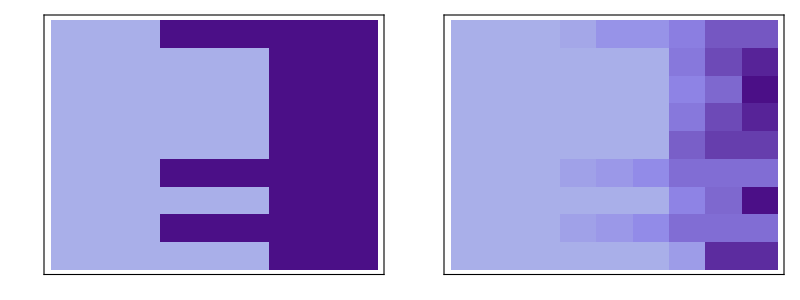

```mathematica
(* Vector of node types*)
nodeType=RandomChoice[Range[networkDimension],sampledCoordinates//Length]
dimensionalPenalizationsMask=Table[penalizationsMatrix[[i,#]]&/@nodeType,{i,nodeType}]; (* Very elegant way of generating full matrix of how we're re-weighting all edges according to the movement Kernel.  This includes both the multitype transition Penalization Mask and the baseline Markov connectivity *)
migrationDimensionalMatrix=(#/Total[#])&/@(dimensionalPenalizationsMask*migrationProbabilities);
(**)
matrixPenalizationsPlot=MatrixPlot[Sort/@dimensionalPenalizationsMask,PlotTheme->"LakeMatrixPlot"];
matrixDimensionalPlot=MatrixPlot[Sort/@migrationDimensionalMatrix,PlotTheme->"LakeMatrixPlot"];
Grid[{{matrixPenalizationsPlot,matrixDimensionalPlot}}]
```

## Synthesizing : Markov Dimensional Network

(0. | 0.27323 | 0.108411 | 0.27323 | 0.186311 | 0. | 0.108411 | 0. | 0.0504074
0.481079 | 0. | 0. | 0. | 0. | 0.328041 | 0. | 0.19088 | 0.
0.231253 | 0. | 0. | 0. | 0. | 0.582832 | 0. | 0.185915 | 0.
0.481079 | 0. | 0. | 0. | 0. | 0.19088 | 0. | 0.328041 | 0.
0.254256 | 0. | 0. | 0. | 0. | 0.372872 | 0. | 0.372872 | 0.
0. | 0.155057 | 0.227394 | 0.0902242 | 0.227394 | 0. | 0.0725357 | 0. | 0.227394
0.231253 | 0. | 0. | 0. | 0. | 0.185915 | 0. | 0.582832 | 0.
0. | 0.0902242 | 0.0725357 | 0.155057 | 0.227394 | 0. | 0.227394 | 0. | 0.227394
0.0844532 | 0. | 0. | 0. | 0. | 0.457773 | 0. | 0.457773 | 0.)

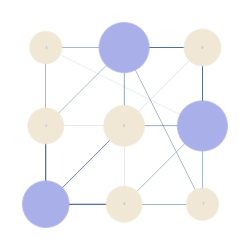

```mathematica
(* Calculate the steady state for our transitions matrix *)
markovPDF=CalculateMarkovSteadyState[migrationDimensionalMatrix];
(* Show the Markov transition matrix*)
MatrixForm[migrationDimensionalMatrix]
(*
Visualization:
  1. Node type is represented by color.
2. Frequency of visit in markov steady state represented by node diameter. 
3. Probability of transition represented by edge thickness
*)
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/networkDimension]];
stylesSwatchType=Directive[Opacity[1],colorsType[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[networkDimension];
stylesListType=(ToString[#[[1]]]->stylesSwatchType[[#[[2]]]])&/@Transpose[{Range[nodeType//Length],nodeType}];
markovDimensional=GraphPlotWrapper[
Chop[migrationDimensionalMatrix//LowerTriangularize,edgeChopThreshold],.1,
Thread[VertexList[originalMap ]->.25*Log[5+7.5*Rescale[markovPDF]]],
stylesListType
]
```

## Ensembles of Trajectories

### Adding in Mosquito Death Transitions

```mathematica
MatrixForm[migrationDimensionalMatrix]
```

(0. | 0.27323 | 0.108411 | 0.27323 | 0.186311 | 0. | 0.108411 | 0. | 0.0504074
0.481079 | 0. | 0. | 0. | 0. | 0.328041 | 0. | 0.19088 | 0.
0.231253 | 0. | 0. | 0. | 0. | 0.582832 | 0. | 0.185915 | 0.
0.481079 | 0. | 0. | 0. | 0. | 0.19088 | 0. | 0.328041 | 0.
0.254256 | 0. | 0. | 0. | 0. | 0.372872 | 0. | 0.372872 | 0.
0. | 0.155057 | 0.227394 | 0.0902242 | 0.227394 | 0. | 0.0725357 | 0. | 0.227394
0.231253 | 0. | 0. | 0. | 0. | 0.185915 | 0. | 0.582832 | 0.
0. | 0.0902242 | 0.0725357 | 0.155057 | 0.227394 | 0. | 0.227394 | 0. | 0.227394
0.0844532 | 0. | 0. | 0. | 0. | 0.457773 | 0. | 0.457773 | 0.)

```mathematica
mosHazardRates = Table[.1,{i,1,Length[sampledCoordinates]}];
```

```mathematica
mosMatrix = Join[Table[Join[migrationDimensionalMatrix[[i]]*(1-mosHazardRates[[i]]),{mosHazardRates[[i]]},1],{i,1,Length[migrationDimensionalMatrix]}],{Join[Table[0,{i,1,Length[migrationDimensionalMatrix]}],{1.}]},1];
```

```mathematica
MatrixForm[mosMatrix]
```

(0. | 0.245907 | 0.0975695 | 0.245907 | 0.16768 | 0. | 0.0975695 | 0. | 0.0453666 | 0.1
0.432971 | 0. | 0. | 0. | 0. | 0.295237 | 0. | 0.171792 | 0. | 0.1
0.208127 | 0. | 0. | 0. | 0. | 0.524549 | 0. | 0.167324 | 0. | 0.1
0.432971 | 0. | 0. | 0. | 0. | 0.171792 | 0. | 0.295237 | 0. | 0.1
0.22883 | 0. | 0. | 0. | 0. | 0.335585 | 0. | 0.335585 | 0. | 0.1
0. | 0.139551 | 0.204655 | 0.0812018 | 0.204655 | 0. | 0.0652821 | 0. | 0.204655 | 0.1
0.208127 | 0. | 0. | 0. | 0. | 0.167324 | 0. | 0.524549 | 0. | 0.1
0. | 0.0812018 | 0.0652821 | 0.139551 | 0.204655 | 0. | 0.204655 | 0. | 0.204655 | 0.1
0.0760079 | 0. | 0. | 0. | 0. | 0.411996 | 0. | 0.411996 | 0. | 0.1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

### Examining a Single Trajectory

```mathematica
(* Start by generating an ensemble *)
init = Table[0,{i,1,Length[mosMatrix]}];
init[[1]]=1;  (* {2,1,1,1,1,2,2,1,1}*)
P = DiscreteMarkovProcess[init,mosMatrix];
RandomSeed[1];
mosEnsemble = RandomFunction[P, {0,100},10];
```

```mathematica
(* Define the Entomological Incubation Period *)
EIP = 10;
```

```mathematica
(* Select a chain *)
chainIndex =4;
mosChain = mosEnsemble["Paths"][[chainIndex]];
(* Restrict to only time steps where the mosquitoes are not dead *)
mosChain = Cases[mosChain,{_,a_}/;a<Length[mosMatrix]]
(* Time of death *)
tDeath = Length[mosChain]
```

{{0,1},{1,4},{2,1},{3,2},{4,1},{5,2},{6,1},{7,2},{8,3},{9,4},{10,1},{11,2},{12,3},{13,2},{14,1},{15,4},{16,1},{17,2},{18,1}}

19

```mathematica
(* Look at the node type at each place visited, just to verify we're alternating *)
pathNodeTypes = (nodeType[[#]]&/@nodeType[[#]])&/@mosChain[[;;,2]];
(* Add the type visited to each row of the mosChain matrix *)
mosChain = Transpose[Join[Transpose[mosChain],{pathNodeTypes}]];
```

```mathematica
(* These are all of the indexes of the relevant starting positions
"Relevant" here means that they occur early enough that the mosquitoes do not die before the end of the EIP *)
tIndexes =  Position[mosChain[[;;Max[tDeath-EIP,1]]], {_,_,1}]//Flatten
```

{2,4,6,8}

```mathematica
(* Count visits to blood feeding sites following an initial infection at each blood feeding site *)
i = tIndexes[[1]]
(* And the initial position *)
j = mosChain[[i,2]]
```

2

4

```mathematica
(* The time steps that occur between end of EIP and mosquito death *)
subMosChain = mosChain[[Min[i+EIP,tDeath + 1];;tDeath]]
(* Find where the secondary infectious occur:
Find the Location of all rows in the subChain where we visit a feeding site *)
bitesMosChain = Cases[subMosChain,{_,_,1}][[;;, 2]]
```

{{11,2,1},{12,3,2},{13,2,1},{14,1,2},{15,4,1},{16,1,2},{17,2,1},{18,1,2}}

{2,2,4,2}

For the example above, we would say that a mosquito who was initially infected at site 3 then lived long enough to bite 2 more people at site 2

```mathematica
(* Repeating, but for the 2nd index *)
(* Count visits to blood feeding sites following an initial infection at each blood feeding site *)
i = tIndexes[[2]]
(* And the initial position *)
j = mosChain[[i,2]]
(* The time steps that occur between end of EIP and mosquito death *)
subMosChain = mosChain[[Min[i+EIP,tDeath + 1];;tDeath]]
(* Find where the secondary infectious occur:
Find the Location of all rows in the subChain where we visit a feeding site *)
bitesMosChain = Cases[subMosChain,{_,_,1}][[;;, 2]]
```

4

2

{{13,2,1},{14,1,2},{15,4,1},{16,1,2},{17,2,1},{18,1,2}}

{2,4,2}

So in addition this same mosquito who bit someone at site 4 lived long enough to also bite someone at site 2.

## Calculate VC-influence matrix

What I call the VC - influence matrix is the number of secondary bites that occur at site j given that the initial bite occurred at site i.  If we sum over all target sites j we obtain the Vectorial Capacity for each site i. 

This matrix will serve as our objective function

As we will see, we can calculate the VCI matrix as long as we only count the very first blood feeding site visited as the origin of all secondary infectious bites.  If we allow for mosquitoes to visit multiple blood feeding sites and attribute the secondary infectious bites that can be attributed to all blood feeding sites visited then we get the proportions right but not the total numbers of secondary bites right.

```mathematica
(* Start by generating an ensemble *)
```

```mathematica
(*init = Table[0,{i,1,Length[mosMatrix]}];
init[[2]]=1.;*)
init=Join[Table[1./Length[nodeType],{i,1,Length[nodeType]}],{0}];
init
P = DiscreteMarkovProcess[init,mosMatrix];
RandomSeed[2];
mosEnsemble = RandomFunction[P, {0,100},100000];
```

{0.111111,0.111111,0.111111,0.111111,0.111111,0.111111,0.111111,0.111111,0.111111,0}

```mathematica
(* Define the Entomological Incubation Period *)
EIP = 10;
```

### Only count the number of secondary bites that follow from the first initial bite

That is to say, count only the visits to blood feeding sites that occur >= EIP time steps following the first visit to a blood feeding site.

```mathematica
(* Initialize VCI, where VCI[[i,j]] = Number of bites at j following an infectious bite at i *)
VCI = Table[0,{i,1,Length[migrationDimensionalMatrix]},{j,1,Length[migrationDimensionalMatrix]}];

Do[
(* Select a chain *)
mosChain = mosEnsemble["Paths"][[chainIndex]];
mosChain = Cases[mosChain,{_,a_}/;a<Length[mosMatrix]];
tDeath = Length[mosChain];
(* Look at the node type at each place visited, just to verify we're alternating *)
pathNodeTypes = (nodeType[[#]]&/@nodeType[[#]])&/@mosChain[[;;,2]];
(* Add the type visited to each *)
mosChain = Transpose[Join[Transpose[mosChain],{pathNodeTypes}]];

(* These are all of the indexes of the relevant starting positions *)
tIndexes =  Position[mosChain[[;;Max[tDeath-EIP,1]]], {_,_,1}]//Flatten;
(* Count visits to blood feeding sites following initial infection at each blood feeding site *)
Do[ (* Loop over all starting indices *)
(* Subset our chain according to the times when secondary infections could occur
Between t = i + EIP and tDeath *)
subMosChain = mosChain[[Min[i+EIP,tDeath + 1];;tDeath]];
(* Find where the secondary infectious occur:
Find the Location of all rows in the subChain where we visit a feeding site *)
bitesMosChain = Cases[subMosChain,{_,_,1}][[;;, 2]]; 
Do[ (* Add biting event counts *)
VCI[[mosChain[[i,2]],bitesMosChain[[j]]]]+=1,
{j,1,Length[bitesMosChain]}]
(* End *)
,{i,tIndexes[[;;Min[Length[tIndexes],1]]]}], (* Right now, only the first *)
(* End loop over chain *)
{chainIndex,1,mosEnsemble["PathCount"]}]
```

```mathematica
(* Visualize the VC-influence matrix*)
MatrixForm[1.*VCI/mosEnsemble["PathCount"]]
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.04946 | 0.04042 | 0.0485 | 0.06282 | 0. | 0.0411 | 0. | 0.05046
0. | 0.04782 | 0.03904 | 0.04676 | 0.06052 | 0. | 0.03736 | 0. | 0.04792
0. | 0.04688 | 0.0392 | 0.04748 | 0.06134 | 0. | 0.03994 | 0. | 0.05152
0. | 0.05728 | 0.0468 | 0.05754 | 0.07336 | 0. | 0.0442 | 0. | 0.05972
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.04608 | 0.03886 | 0.04738 | 0.06072 | 0. | 0.03636 | 0. | 0.05028
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.04954 | 0.04182 | 0.04932 | 0.06546 | 0. | 0.03914 | 0. | 0.05226)

```mathematica
(* Compare to an analytical approximation *)
h = DiagonalMatrix[((init[[;;-2]]*(2.-nodeType))+ (init[[;;-2]]*(nodeType-1.)).ms)].MatrixPower[ms,Ceiling[EIP/2.]*2].Inverse[(IdentityMatrix[Length[ms]] - MatrixPower[ms,1])].DiagonalMatrix[(2-nodeType)];
MatrixForm[h]
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.0499105 | 0.0411968 | 0.0499105 | 0.0643943 | 0. | 0.0411968 | 0. | 0.0524512
0. | 0.0465361 | 0.0384118 | 0.0465361 | 0.060041 | 0. | 0.0384117 | 0. | 0.0489055
0. | 0.0499105 | 0.0411968 | 0.0499105 | 0.0643943 | 0. | 0.0411968 | 0. | 0.0524512
0. | 0.0536648 | 0.0442959 | 0.0536648 | 0.0692384 | 0. | 0.0442959 | 0. | 0.0563971
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.0465361 | 0.0384117 | 0.0465361 | 0.060041 | 0. | 0.0384118 | 0. | 0.0489055
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.0495024 | 0.0408603 | 0.0495024 | 0.0638682 | 0. | 0.0408603 | 0. | 0.052023)

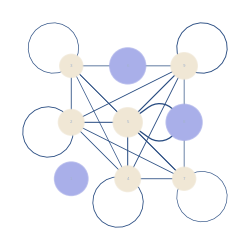

```mathematica
(* Network Visualization of the VC-influence matrix *)
markovPDF=CalculateMarkovSteadyState[migrationDimensionalMatrix];
(**)
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/networkDimension]];
stylesSwatchType=Directive[Opacity[1],colorsType[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[networkDimension];
stylesListType=(ToString[#[[1]]]->stylesSwatchType[[#[[2]]]])&/@Transpose[{Range[nodeType//Length],nodeType}];
markovDimensional=GraphPlotWrapper[
Chop[(10.*VCI/mosEnsemble["PathCount"])//LowerTriangularize,edgeChopThreshold],.1,
Thread[VertexList[originalMap ]->.25*Log[5+7.5*Rescale[markovPDF]]],
stylesListType
]
```

### Count the number of secondary bites that follow from the ALL initial bites

That is to say, count ALL of the visits to blood feeding sites that occur >= EIP time steps after an initial visit to ANY blood feeding site

```mathematica
(* Initialize VCI, where VCI[[i,j]] = Number of bites at j following an infectious bite at i *)
VCI = Table[0,{i,1,Length[migrationDimensionalMatrix]},{j,1,Length[migrationDimensionalMatrix]}];

Do[
(* Select a chain *)
mosChain = mosEnsemble["Paths"][[chainIndex]];
mosChain = Cases[mosChain,{_,a_}/;a<Length[mosMatrix]];
tDeath = Length[mosChain];
(* Look at the node type at each place visited, just to verify we're alternating *)
pathNodeTypes = (nodeType[[#]]&/@nodeType[[#]])&/@mosChain[[;;,2]];
(* Add the type visited to each *)
mosChain = Transpose[Join[Transpose[mosChain],{pathNodeTypes}]];

(* These are all of the indexes of the relevant starting positions *)
tIndexes =  Position[mosChain[[;;Max[tDeath-EIP,1]]], {_,_,1}]//Flatten;
(* Count visits to blood feeding sites following initial infection at each blood feeding site *)
Do[ (* Loop over all starting indices *)
(* Subset our chain according to the times when secondary infections could occur
Between t = i + EIP and tDeath *)
subMosChain = mosChain[[Min[i+EIP,tDeath + 1];;tDeath]];
(* Find where the secondary infectious occur:
Find the Location of all rows in the subChain where we visit a feeding site *)
bitesMosChain = Cases[subMosChain,{_,_,1}][[;;, 2]]; 
Do[ (* Add biting event counts *)
VCI[[mosChain[[i,2]],bitesMosChain[[j]]]]+=1,
{j,1,Length[bitesMosChain]}],
(* End *)
{i,tIndexes}], (* Right now, only the first *)
(* End loop over chain *)
{chainIndex,1,mosEnsemble["PathCount"]}]
```

```mathematica
(* Visualize the VC-influence matrix*)
MatrixForm[1.*VCI/mosEnsemble["PathCount"]]
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.25656 | 0.21234 | 0.25691 | 0.33489 | 0. | 0.21245 | 0. | 0.27345
0. | 0.21672 | 0.17731 | 0.21706 | 0.27967 | 0. | 0.17841 | 0. | 0.23053
0. | 0.26104 | 0.21461 | 0.26298 | 0.33946 | 0. | 0.21501 | 0. | 0.27374
0. | 0.32264 | 0.26296 | 0.32304 | 0.41709 | 0. | 0.26863 | 0. | 0.33882
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.21614 | 0.18074 | 0.21775 | 0.28501 | 0. | 0.18389 | 0. | 0.23568
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.27298 | 0.22246 | 0.2727 | 0.35189 | 0. | 0.22606 | 0. | 0.288)

```mathematica
(* Compare to an analytical approximation *)h = DiagonalMatrix[(init[[;;-2]]*(2.-nodeType) + (init[[;;-2]]*(nodeType-1.)).ms).Inverse[(IdentityMatrix[Length[ms]] - MatrixPower[ms,2])]].MatrixPower[ms,Ceiling[EIP/2.]*2].Inverse[(IdentityMatrix[Length[ms]] - MatrixPower[ms,2])].DiagonalMatrix[(2-nodeType)];
MatrixForm[h]
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.260602 | 0.215105 | 0.260602 | 0.336228 | 0. | 0.215105 | 0. | 0.273868
0. | 0.220389 | 0.181914 | 0.220389 | 0.284347 | 0. | 0.181913 | 0. | 0.23161
0. | 0.260602 | 0.215105 | 0.260602 | 0.336228 | 0. | 0.215105 | 0. | 0.273868
0. | 0.325421 | 0.268608 | 0.325421 | 0.419858 | 0. | 0.268608 | 0. | 0.341989
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.220389 | 0.181913 | 0.220389 | 0.284347 | 0. | 0.181914 | 0. | 0.23161
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.270809 | 0.223531 | 0.270809 | 0.349399 | 0. | 0.223531 | 0. | 0.284598)

```mathematica
(* Simple ratio comparison between simulation and analytic results - looks like we're within a few percent! *)
h[[Position[nodeType,1]//Flatten,Position[nodeType,1]//Flatten]]/(VCI[[Position[nodeType,1]//Flatten,Position[nodeType,1]//Flatten]]/mosEnsemble["PathCount"])
Mean[(h[[Position[nodeType,1]//Flatten,Position[nodeType,1]//Flatten]]/(VCI[[Position[nodeType,1]//Flatten,Position[nodeType,1]//Flatten]]/mosEnsemble["PathCount"]))//Flatten]
```

{{1.01576,1.01302,1.01437,1.00399,1.01249,1.00153},{1.01693,1.02596,1.01534,1.01672,1.01964,1.00469},{0.998324,1.0023,0.990959,0.990478,1.00044,1.00047},{1.00862,1.02148,1.00737,1.00664,0.999918,1.00935},{1.01966,1.00649,1.01212,0.997672,0.989252,0.982732},{0.992046,1.00482,0.993065,0.992921,0.988814,0.988189}}

1.00457

```mathematica
(* Suppressing and replacing complexinfinity: *)
MatrixForm[ReplaceAll[#,Indeterminate->0]&/@Quiet[h/VCI*mosEnsemble["PathCount"]]]
```

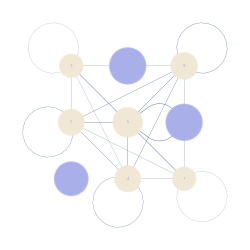

```mathematica
(* Network Visualization of the VC-influence matrix *)
markovPDF=CalculateMarkovSteadyState[migrationDimensionalMatrix];
(**)
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/networkDimension]];
stylesSwatchType=Directive[Opacity[1],colorsType[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[networkDimension];
stylesListType=(ToString[#[[1]]]->stylesSwatchType[[#[[2]]]])&/@Transpose[{Range[nodeType//Length],nodeType}];
markovDimensional=GraphPlotWrapper[
Chop[(.5*VCI/mosEnsemble["PathCount"])//LowerTriangularize,edgeChopThreshold],.1,
Thread[VertexList[originalMap ]->.25*Log[5+7.5*Rescale[markovPDF]]],
stylesListType
]
```

### Some notes one how we can calculate VCI from the Markov Matrix

```mathematica
(* Visualize the VC-influence matrix*)
MatrixForm[1.*VCI/mosEnsemble["PathCount"]]
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.0529 | 0.0464 | 0.0572 | 0.0707 | 0. | 0.0462 | 0. | 0.0547
0. | 0.0419 | 0.0372 | 0.0441 | 0.0549 | 0. | 0.0367 | 0. | 0.045
0. | 0.0501 | 0.0425 | 0.0494 | 0.0681 | 0. | 0.0394 | 0. | 0.0525
0. | 0.0572 | 0.0449 | 0.0594 | 0.0701 | 0. | 0.0491 | 0. | 0.0602
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.0411 | 0.0373 | 0.0439 | 0.06 | 0. | 0.0359 | 0. | 0.049
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.0501 | 0.0411 | 0.0522 | 0.0644 | 0. | 0.0431 | 0. | 0.0522)

```mathematica
(* Compare to an analytical approximation *)
h = DiagonalMatrix[((init[[;;-2]]*(2.-nodeType))+ (init[[;;-2]]*(nodeType-1.)).ms)]. MatrixPower[ms,Ceiling[EIP/2.]*2].
Inverse[(IdentityMatrix[Length[ms]] - ms)].
DiagonalMatrix[(2-nodeType)];
MatrixForm[h]
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.0499105 | 0.0411968 | 0.0499105 | 0.0643943 | 0. | 0.0411968 | 0. | 0.0524512
0. | 0.0465361 | 0.0384118 | 0.0465361 | 0.060041 | 0. | 0.0384117 | 0. | 0.0489055
0. | 0.0499105 | 0.0411968 | 0.0499105 | 0.0643943 | 0. | 0.0411968 | 0. | 0.0524512
0. | 0.0536648 | 0.0442959 | 0.0536648 | 0.0692384 | 0. | 0.0442959 | 0. | 0.0563971
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.0465361 | 0.0384117 | 0.0465361 | 0.060041 | 0. | 0.0384118 | 0. | 0.0489055
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.0495024 | 0.0408603 | 0.0495024 | 0.0638682 | 0. | 0.0408603 | 0. | 0.052023)

How did we come up with that huge expression?  We can divide it up into 4 parts:

```mathematica
(* This is the vector that represents the initial conditions, a superposition of the probability of the first visit to each blood feeding site *)
(init[[;;-2]]*(2.-nodeType)) (* This is all blood feeding nodes *)
(init[[;;-2]]*(nodeType-1.)).ms (* This is all egg laying nodes, where all who start at egg laying nodes need 1 extra step to get to the very first blood feeding node *)
(* Lastly we convert to a diagonal matrix, in order to get out a full matrix VCI and not just a single vector *)
MatrixForm[
 DiagonalMatrix[((init[[;;-2]]*(2.-nodeType))+ (init[[;;-2]]*(nodeType-1.)).ms)]]
```

{0.,0.111111,0.111111,0.111111,0.111111,0.,0.111111,0.,0.111111}

{0.,0.0518511,0.0408341,0.0518511,0.06411,0.,0.0408341,0.,0.0505196}

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.162962 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.151945 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.162962 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.175221 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.151945 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.161631)

```mathematica
(* This is the time delay between reaching the initial blood feeding site and the end of the EIP *)
MatrixForm[
MatrixPower[ms,Ceiling[EIP/2.]*2]]
```

(0.10246 | 0. | 0. | 0. | 0. | 0.123109 | 0. | 0.123109 | 0.
0. | 0.0581922 | 0.0480318 | 0.0581922 | 0.075078 | 0. | 0.0480316 | 0. | 0.0611526
0. | 0.058191 | 0.0480324 | 0.0581908 | 0.0750783 | 0. | 0.0480318 | 0. | 0.0611542
0. | 0.0581922 | 0.0480316 | 0.0581922 | 0.075078 | 0. | 0.0480318 | 0. | 0.0611526
0. | 0.058191 | 0.0480321 | 0.058191 | 0.0750783 | 0. | 0.0480321 | 0. | 0.061154
0.102457 | 0. | 0. | 0. | 0. | 0.123111 | 0. | 0.12311 | 0.
0. | 0.0581908 | 0.0480318 | 0.058191 | 0.0750783 | 0. | 0.0480324 | 0. | 0.0611542
0.102457 | 0. | 0. | 0. | 0. | 0.12311 | 0. | 0.123111 | 0.
0. | 0.0581901 | 0.0480323 | 0.0581901 | 0.0750786 | 0. | 0.0480323 | 0. | 0.0611551)

```mathematica
(* This is an algebraic way of summing over the probabilities of visiting any particular blood feeding site *)
MatrixForm[
Inverse[(IdentityMatrix[Length[ms]] - MatrixPower[ms,1])]]
(* Is derived from summing over the matrix raised to higher and higher powers *)
Sum[x^n,{n,0,∞}]
```

(2.31514 | 0.894701 | 0.623777 | 0.894701 | 0.99153 | 1.47401 | 0.623777 | 1.47401 | 0.708356
1.57531 | 1.74016 | 0.589532 | 0.73252 | 0.911172 | 1.64622 | 0.571287 | 1.51531 | 0.71849
1.33059 | 0.714223 | 1.61596 | 0.69212 | 0.92022 | 1.89253 | 0.563164 | 1.51372 | 0.757471
1.57531 | 0.73252 | 0.571287 | 1.74016 | 0.911172 | 1.51531 | 0.589532 | 1.64622 | 0.71849
1.35312 | 0.706225 | 0.588719 | 0.706225 | 1.91939 | 1.69186 | 0.588719 | 1.69186 | 0.753882
1.22674 | 0.778127 | 0.73838 | 0.716251 | 1.03177 | 2.54843 | 0.590584 | 1.48799 | 0.881727
1.33059 | 0.69212 | 0.563164 | 0.714223 | 0.92022 | 1.51372 | 1.61596 | 1.89253 | 0.757471
1.22674 | 0.716251 | 0.590584 | 0.778127 | 1.03177 | 1.48799 | 0.73838 | 2.54843 | 0.881727
1.18679 | 0.683682 | 0.59494 | 0.683682 | 0.925537 | 1.77503 | 0.59494 | 1.77503 | 1.78038)

1/(1-x)

```mathematica
(* Need one more part to pull out only the columns that correspond to blood feeding sites: *)
MatrixForm[DiagonalMatrix[(2-nodeType)]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
(* And then, to get to the case where we enumerate all secondary bites by summing over all primary bites, all we need to do is further adjust the initial conditions (first term in the sum) to sum over all primary bites *)
DiagonalMatrix[(init[[;;-2]]*(2.-nodeType) + (init[[;;-2]]*(nodeType-1.)).ms).Inverse[(IdentityMatrix[Length[ms]] - MatrixPower[ms,2])]]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.85089,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.719594,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.85089,0.,0.,0.,0.,0.},{0.,0.,0.,0.,1.06253,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.719594,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.884221}}